## Import Data

Use a local copy of the data provided by Christelle Ekosso on 20 July 2023, via Slack/Google Drive;

```mathematica
SeedRandom[1841]; (*set a random seed for training/test set generation for replicability*)
SetDirectory@NotebookDirectory[];
<<"src/platereader.wl"
```

```mathematica
(*some trickiness to merge the files provided in an appropriate way...*)
spectra=With[
{sortedPlateFileNames =SortBy[StringTake[#,-10]&]@FileNames["data/2023_07_20_PH_Indicator/*.txt"]},
Normal@Map[Flatten]@Merge[Join]@Map[importPlateReaderFile]@sortedPlateFileNames];

measuredpH = With[
{dataRows=Join[Range[4,11],Range[16,23],Range[27,34],Range[38,45],Range[49,56],Range[61,68]]},
Import[
"data/2023_07_20_PH_Indicator/20230720 pH Indicator Plates.xlsx",
{"Data",2,dataRows,2;;13},
"EmptyField"->Missing []]//Flatten];

(* handle an extraneous sample in Plate 4, as noted in the data integrity log; this throws off our analysis of the triplicate measurement statistics; for simplicity we will exclude it from all processes *)
measuredpH =measuredpH// With[
{plate = 4, row = 6, col = 10 (*4:F10*)},
With [ 
{position = (plate-1)*96+(row-1)*12+col},
ReplacePart[ position->Missing[]]]];

wavelengths=spectra[[All,1]];
```

```mathematica
(*get data into a list of {spectra}-> pH values*)
normalizeSpectrum[l_?VectorQ]:=Normalize[#,Total]&@(l-Min[l])

output[spectrum_List,pH_?NumericQ]:=(normalizeSpectrum[spectrum]->pH);
output[_,_]:=Nothing;  (*if there is not a Numeric pH value, then drop this entry from both sets *)

(*in the order they are presented...no need to sort by pH*)
data =MapThread[output, {Transpose[spectra[[All,2,All]]],measuredpH}];

results = Association[];
```

## Assess the Performance Limit

### An ideal world

For reference:  If the error was bounded by the distance to the nearest example...how much would our pH error be? (In other words, if we had a perfect classifier that had to put things into the nearest example...and there was no error in our measured pH values, how close would it be)  Assess this by sampling 5 times...

```mathematica
sample=
With[
{ph = data[[All,2]]},
Table[
{train,test}=ResourceFunction["TrainTestSplit"][ph];
pred=Flatten[ First/@Nearest[train]/@test];
{Mean@Abs[test-pred],Correlation[test,pred]^2},
{i,5}]];
results["pH Sampling Limit"]=Around/@Transpose[sample]
```

{0.01640.0025,0.9999160.000020}

We can also try to assess this by looking at the distance that any individual pH is from the closest pH in the dataset:

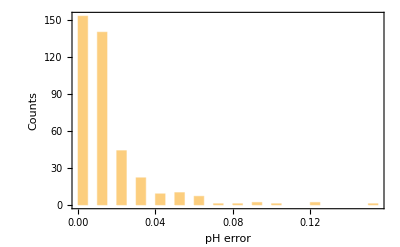

```mathematica
closest=With[
{pH = data[[All,2]]},
Last/@Nearest[pH->"Distance",pH, 2]];

Histogram[closest,
PlotRange->All,
Frame->True,FrameLabel->{"pH error", "Counts"}]
```

Alternatively, quantify this with the cumulative distribution function:  95% of the time, we are less than 0.05 pH units away.

0.05

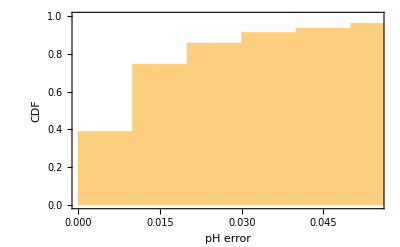

```mathematica
Quantile[closest,0.95]

Histogram[closest,Automatic,"CDF",
Frame->True,FrameLabel->{"pH error", "CDF"}]
```

### Variations present in the Triplicate Trials

A nice aspect of this dataset is that each experiment is repeated in triplicate!  We group these (before we sort things) and then we can evaluate statistics.  As we are evaluating our models by the mean absolute deviation (MAD) between the predicted and “true” values, it seems only fair to do the same here; we assume the “true” value of each triplicate is the mean of the 3 examples, and then compute the MAD from that.  Computing R^2 doesn’t really make sense here, because there is only one “true” value for each of the 3 points

```mathematica
groupTriplicates=Partition[#,3]&@DeleteMissing@measuredpH;
stdDevTriplicates=StandardDeviation/@groupTriplicates;
madTriplicates = Mean[Abs[(#-Mean[#])]]&/@groupTriplicates;
```

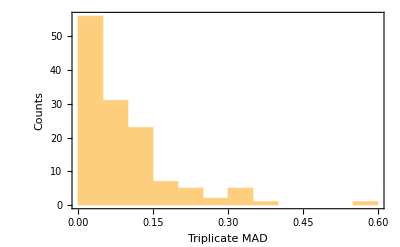

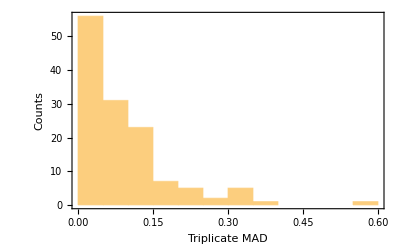

{0.090.09,Missing[]}

```mathematica
Histogram[madTriplicates,
Frame->True,FrameLabel->{"Triplicate MAD","Counts"},
PlotRange->All]

Histogram[madTriplicates,
Frame->True,FrameLabel->{"Triplicate MAD","Counts"}]

results["Triplicate Variation Limit"]={Around[madTriplicates],Missing[]}
```

Comment: Plate 4, F10 corresponds to a “fourth” entry in the triplicate; as noted above, we have dropped this point, after discussing with Christelle E. 

Comment:  There is still one entry with a large MAD

```mathematica
PositionLargest@madTriplicates
```

{71}

```mathematica
groupTriplicates[[71]]
stdDevTriplicates[[71]]
```

{10.81,9.41,10.67}

0.77106

## Approach 0: Naive Regressor Model

Motivation:  Don’t do any data processing or dimensionality reduction and just use some

```mathematica
crossValidate[data_,modelType_String]:=ResourceFunction["CrossValidateModel"][
data,
Predict[#,Method->modelType]&,
"ValidationFunction"->{Automatic,{"MeanDeviation","RSquared"}}
]

summarize[data_,method_String]:=With[
{summary = crossValidate[data,method]},
Around/@Transpose@summary[[All,"ValidationResult"]]]

regressors = {"LinearRegression","NearestNeighbors","RandomForest","GradientBoostedTrees"};

Scan[
(results[#]=summarize[data,#])&,
regressors ]
```

How are we doing so far?

```mathematica
Dataset@results
```

## Approach 1: Principal Components Analysis

Motivation:  Perform principal components analysis to reduce the dimensionality of the problem, then use either linear regression or a nearest-neighbor model to assign the pH.

```mathematica
pca=DimensionReduction[data[[All,1]],Method->"PrincipalComponentsAnalysis"]
transformedData=Table[(pca[entry[[1]]]->entry[[2]]), {entry, data}];
```

DimensionReducerFunction[…]

```mathematica
Scan[
(results[#<>"+ PCA"]=summarize[transformedData,#])&,
regressors ]

Dataset[results]
```

Conclusion:  PCA doesn’t help us tremendously...we’ve now go enough examples to learn from the data

## Approach 2: Optimal Transport Classifier

Concept:  Try to find the most similar spectrum (by Earth Mover Distance, aka W1 Wasserstein metric) and assign that pH to the unknown spectrum.

Further reading:
See:  https://en.wikipedia.org/wiki/Earth_mover%27s_distance
See: JCP 2021 https://doi.org/10.1063/5.0069681
See: JCP 2022 https://doi.org/10.1063/5.0087385

```mathematica
<<"src/emd.wl" (*import the earth mover distance code*)
```

```mathematica
(* define a function for model validation during CV, as EMD is not a built-in classifier *)
validation[model_NearestFunction,validationData_List]:=With[
{obs=validationData[[All,2]],
predicted = model/@validationData[[All,1]]//Flatten},
{Mean@Abs[obs-predicted], Correlation[obs,predicted]^2}]

(* perform 5-fold cross validation of the EMD model *)
cvEMDSummary=ResourceFunction["CrossValidateModel"][
data,
Nearest[#,DistanceFunction->emd]&, (*model definition*)
"ValidationFunction"->validation,
"ParallelQ"->True];

(* collect summary statistics *)
results["EMD"]=Around/@Transpose@%[[All,"ValidationResult"]]
```

{0.230.04,0.9840.007}

Comment:  The naïve EMD implementation is a bit slow after you have about 100 examples in the dataset, as it is brute forcing all the pairwise comparisons (ugh, quadratic scaling).  Running cross validation with the full dataset takes about 10 minutes on my laptop (but part of this is definitely my laptop thermal throttling itself, and part of it is dividing 5 tasks over 4 kernels, so we hang on the remaining job). There are smarter ways to do this calculation, if we want to go down this path in the future ...

## Discussion items and next steps

```mathematica
Dataset@Sort@results
```

With this enlarged dataset of 393 examples (or more properly...with a sample of 80% of this, i.e., 314 training spectra and 79 validation spectra), we can can easily make predictions at  +/-0.25 pH units;  this is about 2x the variation of measured pH within triplicates

The advantage of using the EMD vanishes as we get more examples; simple GBT and/or Nearest Neighbor methods on the normalized spectra does about as well

PCA doesn’t help us (or stated another way, GBT and k-NN can use it and do almost as good as if they have the whole spectrum, but it doesn’t reduce the prediction error)